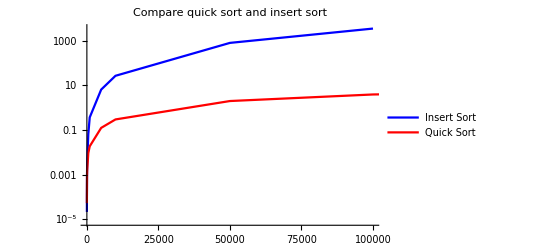

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

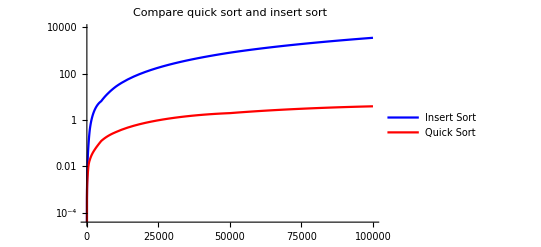

```mathematica
file= OpenRead["c:\\users\petr\desktop\sorting\log.txt"];
filelist= ReadList[file,String];
quickSortResults = filelist[[2;;;;3]];
insertSortResults = filelist[[1;;;;3]];
insertSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,insertSortResults][[;;-4]];
quickSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,quickSortResults];
insertSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,insertSortResults];
quickSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,quickSortResults];
Show[ListLogPlot[insertSortResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Insert Sort"},PlotLabel->"Compare quick sort and insert sort"],ListLogPlot[quickSortResults,Joined->True,PlotStyle->Red,PlotLegends->{"Quick Sort"}]]
insertFunc = Interpolation[insertSortResults];
quickFunc = Interpolation[quickSortResults];
x = LogPlot[{insertFunc[x],quickFunc[x]},{x,0,10^5},PlotStyle->{Blue,Red},PlotLegends->{"Insert Sort","Quick Sort"},PlotLabel->"Compare quick sort and insert sort"]
```

```mathematica
x = Export["test.gif",x,ImageSize->2048]
```

test.gif